```mathematica
(* ZAD.1. 
Dla zadanego ciągu n={1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}} znajdź:
a) pierwszy element, ostatni element, oraz element 4-ty.
b)utwórz nowy ciąg 'x' przez dodanie na początek ciągu n element 'kolor'
c) utwórz nowy ciąg 'g' skaldajacy sie z pierwszych czterech elementów ciągu 'n' raz ostatniego elementu ciągu 'x'.
d) połącz ciągi 'g' oraz 'n' w jeden ciąg 'h'
e) utwórz nowy ciąg 'k', którego elementami będzie 90 pierwszych liczb naturalnych
f) Utwórz macierz o nazwie 'f' o wymiarze 3x3, której elementami są dowolne liczby rzeczywiste. Dla macierzy 'f' wyznacz: wymiar, macierz odwrotną,wyznacznik, pokaż element (2,2) tej macierzy. Wyznacz macierz m=2/3*f/5 
*)
n={1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}} (*a*)
```

```mathematica
{1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}}
```

```mathematica
First[n](*a*)
```

1

```mathematica
Last[n](*a*)
```

{1,2,3}

```mathematica
x={"kolor",1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}}
```

```mathematica
x = Prepend[n,"kolor"](*b*)
```

{kolor,1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}}

```mathematica
g=Take[n,4] ~Join~ {Last[x]}(*c*)

h = g ~Join~ n (*d*)
```

{1,{1,1,1},3,{0.5,-3},{1,2,3}}

{1,{1,1,1},3,{0.5,-3},{1,2,3},1,{1,1,1},3,{0.5,-3},{5,3},{1,2,3}}

```mathematica
k = Range[90] (*e*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

```mathematica
f= {{1,2,3},{4,5,6},{7,8,9}} (*f*)
wymiarF = Dimensions[f]
odwrotnaF = Inverse[f]
detF = Det[f]
elemenet22F = f[[2,2]]
m=2/3*f/5
```

{{1,2,3},{4,5,6},{7,8,9}}

{3,3}

Inverse::sing: Matrix {{1,2,3},{4,5,6},{7,8,9}} is singular.

Inverse[{{1,2,3},{4,5,6},{7,8,9}}]

0

5

{{2/15,4/15,2/5},{8/15,2/3,4/5},{14/15,16/15,6/5}}

```mathematica
(* ZAD.2. 

Dla wektora A = {3,-2,1} oraz B = {8,1,8}. Wyznacz iloczyn skalarny i wektorowy dla tych wektorów. Pokać,że:
Wykaż, że A∘(A×B)=0. 

*)
A = {3,-2,1}
B = {8,1,8}
skalarny = Dot[A,B]
wektorowy = Cross[A,B]
wykazanie  = Simplify Dot[A,Cross[A,B]]
```

{3,-2,1}

{8,1,8}

30

{-17,-16,19}

0

```mathematica
(* ZAD.3. 
1) Wyznacz zbiór 'Y' składający się z 15-tu pseudolosowych liczb całkowitych z przedzialu <-1500,1500>. 
      
   2) Znajdz minimum i maksimum dla zbioru 'Y'.
      3) Wyznacz pierwiastek 6-go stopnia liczby π z dokladnoscią do 100 miejsc po przecinku. 
           4) Za pomocą funkcji 'Table[]' wyznacz wszystkie liczby parzyste za zbioru <1,200>
*)
```

```mathematica
Y = RandomInteger[{-1500,1500},15] (*1*)
min = Min[Y](*2*)
max = Max[Y](*2*)

pi = N[Pi^(1/6),100]
parzyste = Table[i,{i,2,200,2}]
```

{1005,1033,-1164,829,357,141,-987,-1129,848,750,-1478,1348,-961,1029,964}

-1478

1348

1.210203242253764275966030761759943531052762555136318104673056437806462400448143514791134200619603035

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200}

```mathematica
(*  ZAD.4.  
   a) Wyznacz wymiar ponizszej macierzy.
     b) Ile czasu trwa policzenie wyznacznika tej macierzy na twoim komputerze? 
  ({{-x, 2, 3, 4, -7, 8, 8, 8, -1, 3, 3, 3, -5, 3, 2}, {6, 2-x, 8, 7, 9, -8, 6, 8, 7, 6, 8, 8, 9, -1, -1}, {-1, -1, 5-x, -2, -4, 3, x, x, x, 7, -2, -5, 2, 2, 3}, {9, 9, 8, 4-x, 4, 5, 7, -2, 9, x, 3, 3, 2, -2, -2}, {-5, -5, 6, 7, 10-x, 3, 4, 2, 9, 5, 4, 3, 5, 2, 4}, {3, -6, 4, 7, 7, -x, 7, 7, 7, 4, 2, 7, 3, 9, 1}, {-3, -3, 3, 3, 1, 1, 6-x, -2, 1, 9, 2, -4, 4, 6, x}, {5, 5, 6, 7, 3, 2, 5, 2, 4, 5, 3, 5, 4, 6, 3}, {8, -4, 4, x x, 5, 7, 6, x-4, 7, 4, -5, 7, 4, 5, 3}, {5, 3, 7, 6, 5, 7, 6, x, x-8, x-3, x^32-7, 5, 7, 0, -6}, {6, 3, 3, 1000!, 4, 5, -5, 9, -9, -5, 4, 7, 8, 9, x^4}, {3, 6, 7, 9, x, 9, 5, 8, 3, x, 4, 0, x-3, 2-x, 5}, {4, 8, 3, 9, 5, 5, 4, 9, 3, 8, 6, 8, 4, 3, 9-x}, {4, 111!, 5, 4, -8, 4, -4, 10, 3, -8, 3, 3 x, 7, -7, 93}, {4, 3, 5, 3, 5, 2, 6, -2, 6, 2, 6, x-2, 2, 4, -1}})
*)
```

Syntax::bktmcp: Expression "{-x," has no closing "}".

```mathematica
(*
ZAD.5
Narysować trzy funkcje na jednym wykresie: y=sin(x), y=2x, y=x^3-1 w przedziale od -2Pi do 2Pi.  
Narysować linie siatki.
Nazwać wykres "To mój wykres"
Wykres ma mieć dookoła ramkę.
Kolory odpowiednio: czerwony, zielony, niebieski

*)
Clear[f1,f2,f3]
```

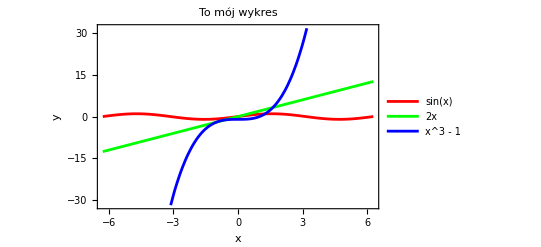

```mathematica
f1[x_]:=Sin[x]
f2[x_]:=2 x
f3[x_]:=x^3-1

Plot[{f1[x],f2[x],f3[x]},{x,-2 Pi,2 Pi},PlotLegends->{"sin(x)","2x","x^3 - 1"},AxesLabel->{"x","y"},PlotStyle->{Red,Green,Blue},Frame->True,FrameLabel->{"x","y"},FrameStyle->Directive[Black,Thick],PlotLabel->"To mój wykres"]
```